# Impulse Response

```mathematica
accelData=Import["C:\\Users\\ambik\\Desktop\\ImpulseInput.xls",{"Data",1}]
```

{{Time (s),Linear Acceleration x (m/s^2),Linear Acceleration y (m/s^2),Linear Acceleration z (m/s^2),Absolute acceleration (m/s^2)},{0.0499597,-0.0319996,-0.00270207,0.000562502,0.0321184},5527,{55.1707,-0.0490635,0.0554145,-0.0286753,0.0793742}}
 |  |  |  |

```mathematica
rawplotData=Transpose[{accelData[[All,1]],accelData[[All,4]]}]
```

{{Time (s),Linear Acceleration z (m/s^2)},{0.0499597,0.000562502},{0.0599307,-0.0280339},{0.0699027,-0.00842759},5522,{55.1408,0.0321451},{55.1508,0.00452224},{55.1608,0.000874159},{55.1707,-0.0286753}}
 |  |  |  |

```mathematica
plotData=rawplotData[[2;;]]
```

{{0.0499597,0.000562502},{0.0599307,-0.0280339},{0.0699027,-0.00842759},{0.0798737,-0.0150116},5521,{55.1408,0.0321451},{55.1508,0.00452224},{55.1608,0.000874159},{55.1707,-0.0286753}}
 |  |  |  |

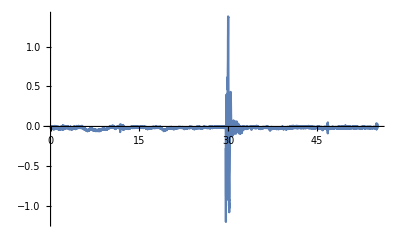

```mathematica
accelPlot=ListLinePlot[plotData,PlotRange->{All,All}]
```

```mathematica
usefulAccelData=Transpose[plotData[[2980;;3300]]][[2]];
```

```mathematica
tf=(3300-2980)*0.01
```

3.2

```mathematica
time=Range[0,tf,0.01];
```

```mathematica
usefulData=Transpose[{time,usefulAccelData}];
```

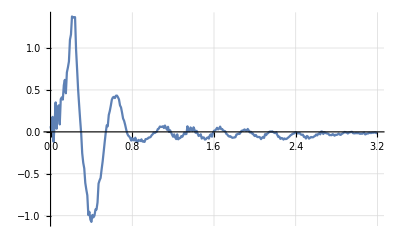

```mathematica
zddotPlotImpulse=ListLinePlot[usefulData,PlotRange->All,GridLines->Automatic]
```

```mathematica
SetAttributes[{A1,A2,b,c,ωn,ωd,ζ},Constant]
```

```mathematica
x[t]=Exp[-ζ ωn t](A1 Cos[ωd t]+A2 Sin[ωd t])
```

ⅇ^(-0.140841 t ωn) (A1 Cos[t ωd]+A2 Sin[t ωd])

```mathematica
Dt[Dt[x[t],t],t]//Simplify
```

ⅇ^(-0.140841 t ωn) ((-1. A1 ωd^2-0.281681 A2 ωd ωn+0.0198361 A1 ωn^2) Cos[t ωd]+(-1. A2 ωd^2+0.281681 A1 ωd ωn+0.0198361 A2 ωn^2) Sin[t ωd])

```mathematica
A1=.;A2=.;b=.;c=.;
```

```mathematica
ωn=.;ζ=.;
```

```mathematica
fitParam=FindFit[(usefulData), { Exp[-b t](( Cos[c t])(-A1 c^2 -2 A2 b c +A1 b^2)+( Sin[c t])(-A2 c^2 +2 A1 b c +A2 b^2))},{A1,A2,b,c},t,MaxIterations->1000000]//Chop
```

{A1→0.00641119,A2→-0.005293,b→1.78688,c→12.5608}

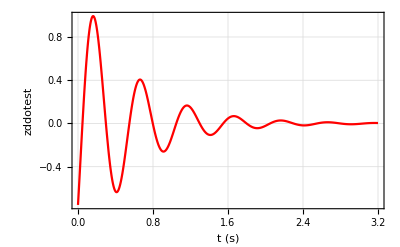

```mathematica
fitPlotImpulse=Plot[Exp[-b t](( Cos[c t])(-A1 c^2 -2 A2 b c +A1 b^2)+( Sin[c t])(-A2 c^2 +2 A1 b c +A2 b^2))//.fitParam,{t,0,tf},PlotRange->All,PlotStyle->{Red},Frame->True,GridLines->Automatic, FrameLabel->{"t (s)","zddotest"}]
```

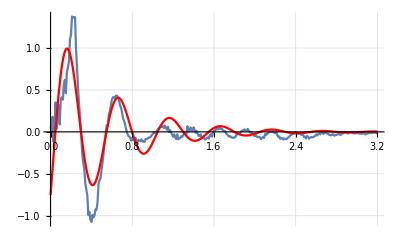

```mathematica
Show[zddotPlotImpulse,fitPlotImpulse]
```

```mathematica
Bcoeff= b/.fitParam
```

1.78688

```mathematica
Ccoeff=c/.fitParam
```

12.5608

```mathematica
eqn1=Bcoeff==ζ ωn
eqn2= Ccoeff== ωn Sqrt[1-ζ^2]
```

1.78688==ζ ωn

12.5608==√(1-ζ^2) ωn

```mathematica
solImpulse=Solve[{eqn1,eqn2},{ζ,ωn}]//First
```

{ζ→0.140841,ωn→12.6873}

```mathematica
eqn3= ωn==Sqrt[k/m]/.solImpulse
```

12.6873==√(k/m)

```mathematica
KsolImpulse=Solve[eqn3,k]/.{m-> 1200}//First(*N/m*)
```

{k→193160.}

# Step Response Data

```mathematica
accelData=Import["C:\\Users\\ambik\\Desktop\\StepInputNew.xls",{"Data",1}]
```

{{Time (s),Linear Acceleration x (m/s^2),Linear Acceleration y (m/s^2),Linear Acceleration z (m/s^2),Absolute acceleration (m/s^2)},6581,{65.6594,-0.139314,0.147269,-0.0509082,0.209017}}
 |  |  |  |

```mathematica
rawplotData=Transpose[{accelData[[All,1]],accelData[[All,4]]}]
```

{{Time (s),Linear Acceleration z (m/s^2)},{0.0473149,-0.0203027},{0.0572849,-0.0135895},{0.0672549,-0.00730785},6575,{65.6295,-0.0117319},{65.6394,-0.038063},{65.6494,-0.0219885},{65.6594,-0.0509082}}
 |  |  |  |

```mathematica
plotData=rawplotData[[2;;]]
```

{{0.0473149,-0.0203027},{0.0572849,-0.0135895},{0.0672549,-0.00730785},{0.0772249,-0.0109916},6574,{65.6295,-0.0117319},{65.6394,-0.038063},{65.6494,-0.0219885},{65.6594,-0.0509082}}
 |  |  |  |

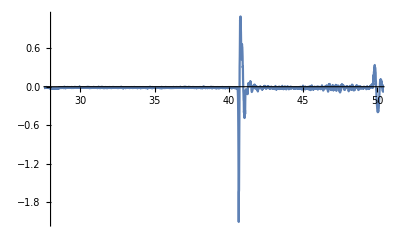

```mathematica
accelPlot=ListLinePlot[plotData,PlotRange->{{28,50},All}]
```

```mathematica
usefulAccelData=Transpose[plotData[[4095;;4300]]][[2]];
```

```mathematica
tf=(4300-4095)*0.01
```

2.05

```mathematica
time=Range[0,tf,0.01];
```

```mathematica
usefulData=Transpose[{time,usefulAccelData}];
```

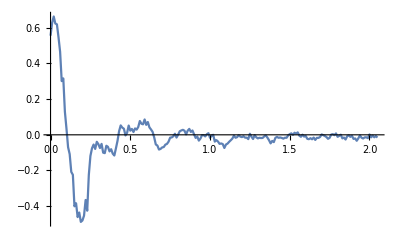

```mathematica
zddotPlotUnit=ListLinePlot[usefulData,PlotRange->All]
```

# Canonical 2nd order Transfer Function

Fitting Transfer function from Impulse Input data to the Unitstep response.

```mathematica
kdc=1/(m s^2+ b s + K)/.{s-> 0,K-> k/.KsolImpulse}
```

5.17705×10^-6

```mathematica
ζ= ζ/.solImpulse
Subscript[ω, n]=ωn/.solImpulse
Subscript[k, dc]= kdc
```

0.140841

12.6873

5.17705×10^-6

```mathematica
Gs=( Subscript[k, dc](Subscript[ω, n])^2/(s^2+2ζ Subscript[ω, n] s +( Subscript[ω, n])^2))
```

0.000833333/(160.967+3.57377 s+s^2)

```mathematica
resUnit=OutputResponse[TransferFunctionModel[Gs,s],80*9.81UnitStep[t],t]
```

{(0.+0. ⅈ)+0.00406295 ⅇ^((-1.78688-12.5608 ⅈ) t) (-1. ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]-(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]+1. 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]-0.142259 ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]+(3.63891×10^-17+0.510119 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]-(3.63891×10^-17+0.510119 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-0.0202375 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])}

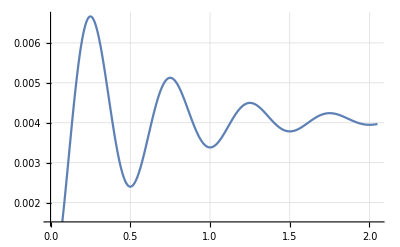

```mathematica
Plot[resUnit,{t,0,tf},GridLines->Automatic]
```

```mathematica
velresUnit=Dt[resUnit,t]
```

{0.00406295 ⅇ^((-1.78688-12.5608 ⅈ) t) (-1. ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])-(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+1. 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 (Piecewise[{{Indeterminate, t==0}, {0, True}}])-0.142259 ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]+(3.63891×10^-17+0.510119 ⅈ) ⅇ^(1.78688 t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-(3.63891×10^-17+0.510119 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-0.0202375 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]^2-(1.78688+12.5608 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(6.1597×10^-16+6.4075 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]-(5.75043×10^-17+6.4075 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(1.78688+12.5608 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]+(12.5608-1.78688 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]-(1.05191×10^-15-0.911523 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]+(12.815-0.911523 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-25.63 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] Sin[12.5608 t] UnitStep[t]-(0.0361621+0.2542 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])-(0.00726002+0.0510339 ⅈ) ⅇ^((-1.78688-12.5608 ⅈ) t) (-1. ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]-(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]+1. 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]-0.142259 ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]+(3.63891×10^-17+0.510119 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]-(3.63891×10^-17+0.510119 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-0.0202375 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])}

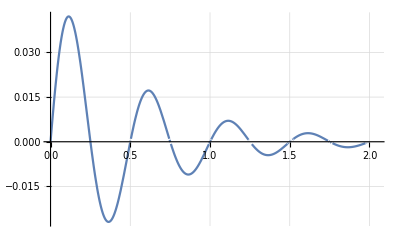

```mathematica
Plot[velresUnit,{t,0,tf},GridLines->Automatic]
```

```mathematica
acclresUnit=Dt[velresUnit,t]
```

{(-0.01452-0.102068 ⅈ) ⅇ^((-1.78688-12.5608 ⅈ) t) (-1. ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])-(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+1. 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 (Piecewise[{{Indeterminate, t==0}, {0, True}}])-0.142259 ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]+(3.63891×10^-17+0.510119 ⅈ) ⅇ^(1.78688 t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-(3.63891×10^-17+0.510119 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-0.0202375 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]^2-(1.78688+12.5608 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(6.1597×10^-16+6.4075 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]-(5.75043×10^-17+6.4075 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(1.78688+12.5608 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]+(12.5608-1.78688 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]-(1.05191×10^-15-0.911523 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]+(12.815-0.911523 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-25.63 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] Sin[12.5608 t] UnitStep[t]-(0.0361621+0.2542 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])-(0.628054-0.182383 ⅈ) ⅇ^((-1.78688-12.5608 ⅈ) t) (-1. ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]+(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]-(8.89219×10^-17+2.22305×10^-17 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]+1. 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]-0.142259 ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]+(3.63891×10^-17+0.510119 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]-(3.63891×10^-17+0.510119 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-0.0202375 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])+0.00406295 ⅇ^((-1.78688-12.5608 ⅈ) t) ((-4.57377-25.1216 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+(1.32086×10^-15+12.815 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])-(2.03931×10^-16+12.815 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}])+(4.57377+25.1216 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 (Piecewise[{{Indeterminate, t==0}, {0, True}}])+(24.9793-3.57377 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-(2.06743×10^-15-2.33316 ⅈ) ⅇ^(1.78688 t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]+(25.63-2.33316 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-51.26 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]-(0.0925618+0.508399 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) Sin[12.5608 t]^2+(315.547-44.8894 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] UnitStep[t]-(1.21121×10^-14-22.8989 ⅈ) ⅇ^(1.78688 t) Cos[12.5608 t] UnitStep[t]+(321.933-22.8989 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Cos[12.5608 t] UnitStep[t]-(476.514-44.8894 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t]^2 UnitStep[t]+(44.8894+315.547 ⅈ) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t] UnitStep[t]-(9.61671×10^-15+78.8546 ⅈ) ⅇ^(1.78688 t) Sin[12.5608 t] UnitStep[t]+(45.7978+400.788 ⅈ) ⅇ^((1.78688+25.1216 ⅈ) t) Sin[12.5608 t] UnitStep[t]-(91.5956+643.867 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Cos[12.5608 t] Sin[12.5608 t] UnitStep[t]+(325.062-0.90845 ⅈ) 2.71828^(1.78688 t) ⅇ^((0.+12.5608 ⅈ) t) Sin[12.5608 t]^2 UnitStep[t])}

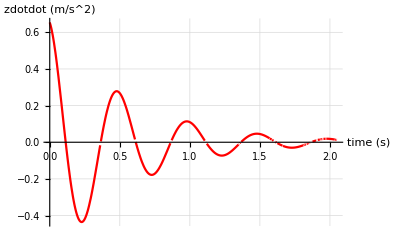

```mathematica
acclResUnitPlot=Plot[acclresUnit,{t,0,tf},PlotRange->All,GridLines->Automatic,AxesLabel->{"time (s)", "zdotdot (m/s^2)" },PlotStyle->Red]
```

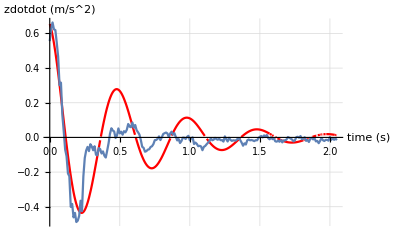

```mathematica
Show[acclResUnitPlot,zddotPlotUnit]
```

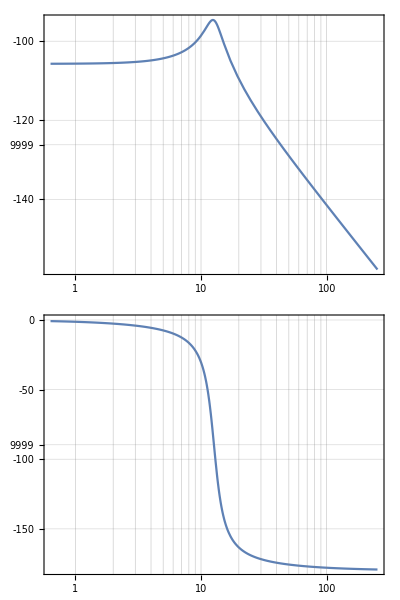

```mathematica
BodePlot[Gs,GridLines->Automatic,StabilityMarginsStyle->{Red,Green}]
```

```mathematica
{gm,pm}=GainPhaseMargins[TransferFunctionModel[Gs,s]]
```

{{{None,∞}},{{None,∞}}}

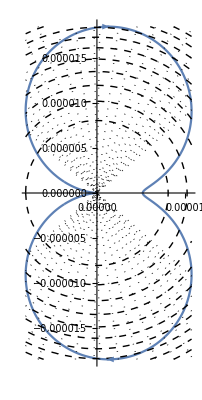

```mathematica
NyquistPlot[TransferFunctionModel[Gs,s],StabilityMargins->{gm,pm},StabilityMarginsStyle->{Directive[Red,Thick],Directive[Green,Thick]},PlotRange->All,NyquistGridLines->Automatic]
```

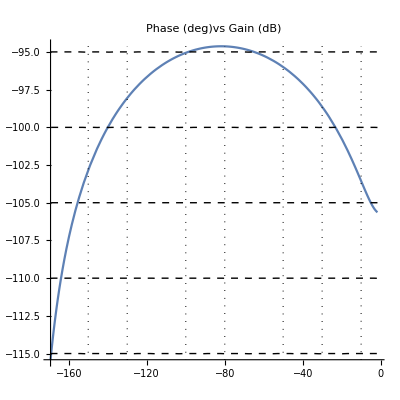

```mathematica
NicholsPlot[TransferFunctionModel[Gs,s],PlotLabel->"Phase (deg)vs Gain (dB)",NicholsGridLines->Automatic,PlotRange->All]
```

```mathematica
resImpulse=OutputResponse[TransferFunctionModel[Gs,s],80*9.81DiracDelta[t],t]
```

{(0.+0. ⅈ)+0.000833333 ⅇ^(-1.78688 t) ((0.+0. ⅈ)+(5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] HeavisideTheta[t]+(62.4801-6.00637×10^-15 ⅈ) HeavisideTheta[t] Sin[12.5608 t])}

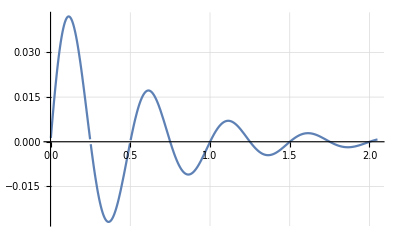

```mathematica
Plot[resImpulse,{t,0,tf},GridLines->Automatic]
```

```mathematica
velresImpulse=Dt[resImpulse,t]
```

{0.000833333 ⅇ^(-1.78688 t) ((5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] DiracDelta[t]+(784.8-7.54449×10^-14 ⅈ) Cos[12.5608 t] HeavisideTheta[t]+(62.4801-6.00637×10^-15 ⅈ) DiracDelta[t] Sin[12.5608 t]-(6.84017×10^-14-2.73607×10^-13 ⅈ) HeavisideTheta[t] Sin[12.5608 t])-0.00148907 ⅇ^(-1.78688 t) ((0.+0. ⅈ)+(5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] HeavisideTheta[t]+(62.4801-6.00637×10^-15 ⅈ) HeavisideTheta[t] Sin[12.5608 t])}

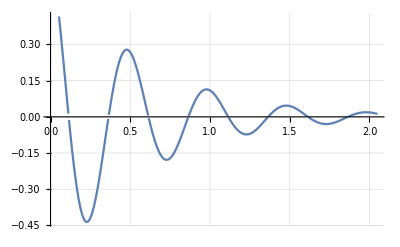

```mathematica
Plot[velresImpulse,{t,0,tf},GridLines->Automatic]
```

```mathematica
acclresImpulse=Dt[velresImpulse,t]
```

{-0.00297814 ⅇ^(-1.78688 t) ((5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] DiracDelta[t]+(784.8-7.54449×10^-14 ⅈ) Cos[12.5608 t] HeavisideTheta[t]+(62.4801-6.00637×10^-15 ⅈ) DiracDelta[t] Sin[12.5608 t]-(6.84017×10^-14-2.73607×10^-13 ⅈ) HeavisideTheta[t] Sin[12.5608 t])+0.00266079 ⅇ^(-1.78688 t) ((0.+0. ⅈ)+(5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] HeavisideTheta[t]+(62.4801-6.00637×10^-15 ⅈ) HeavisideTheta[t] Sin[12.5608 t])+0.000833333 ⅇ^(-1.78688 t) ((1569.6-1.5089×10^-13 ⅈ) Cos[12.5608 t] DiracDelta[t]-(8.5918×10^-13-3.43672×10^-12 ⅈ) Cos[12.5608 t] HeavisideTheta[t]-(1.36803×10^-13-5.47213×10^-13 ⅈ) DiracDelta[t] Sin[12.5608 t]-(9857.72-9.47648×10^-13 ⅈ) HeavisideTheta[t] Sin[12.5608 t]+(5.44564×10^-15-2.17826×10^-14 ⅈ) Cos[12.5608 t] DiracDelta'[t]+(62.4801-6.00637×10^-15 ⅈ) Sin[12.5608 t] DiracDelta'[t])}

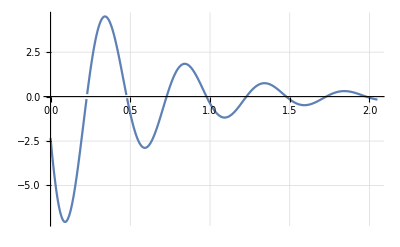

```mathematica
Plot[acclresImpulse,{t,0,tf},GridLines->Automatic]
```